```mathematica
(*@Return {cleanedDat, its length, its min time, its max time}: a cleaned, sorted data list of elements of time*)
cleanRawData[rawData_]:=Module[
{dat},
dat=Select[rawData,#[[1]]<40000&];
dat=#[[1]]&/@dat;
dat=Sort[dat];
{dat, Length[dat],Min[dat],Max[dat]}
];
```

```mathematica
(*This is almost the same function as above (which is legacy code so can only be found in muon_play.nb.), except that we can choose the starting time delimter and the
ending time delimiter. Therefore it can somehow be more flexible.
Return: {distList, binWdith, numBin}*)
```

```mathematica
getDist[data_,startTime_, endTime_,numBin_]:=Module[
{binWidth,hisDat,delimits,counts,trueEndTime,trueStartTime, distList,i,lenCounts},

(*This expression ensures that the endTime will always be binned.*)
binWidth=Ceiling[(endTime-startTime+1)/numBin];

(*Now I want to determine the true suitable endTime given the bin width.
Therefore, we will always guarantee to have the number of bins as initially intended.
Therefore, this function should always function exactly the same as the previous one,
when startTime was set to be Min[data].*)
trueStartTime=startTime;
If[Mod[endTime - startTime,binWidth]==0,
trueEndTime=endTime,
trueEndTime=startTime+binWidth*numBin];

hisDat= HistogramList[data,{trueStartTime,trueEndTime,binWidth}];
delimits=hisDat[[1]];
counts=hisDat[[2]];
lenCounts=Length[counts];
(*Print[lenCounts];*)

(*Now we want to settle delimits and counts into a distribution list of element {startTime, numCounts}*)
distList={};
(*Print["Hey"];
Print[i];
Print[Length[counts]];*)
For[i=1,i≤lenCounts,i++,
(*Print[i];*)
AppendTo[distList,{delimits[[i]],counts[[i]]}];
(*Print[i,": ",distList];*)
];
{distList, binWidth,numBin}
]
```

```mathematica
(*Obtain the estimated error from an experimental value*)
getErr[count_]:=√count;
```

```mathematica
(*Similar to getLogList except that we only get the original count districution instead of log of count.*)
getDistList[cleanData_,startTime_,endTime_, numBin_]:=Module[
{truncDist,binWidth,errList},

(*truncDist is a distribution list of {time, counts} that truncates some early times and late times.*)
{truncDist,binWidth}=getDist[cleanData,startTime, endTime,numBin][[1;;2]];

(*Obtain the error list for truncDist*)
errList={#[[1]],getErr@#[[2]]}&/@truncDist;

{truncDist,binWidth,errList}
];
```

```mathematica
(*Notice that this function will only select counts that are larger than or equal to 2. Data not meeting this requirement will be discarded.
@return {truncDist, binWidth, logErrList}
truncDist: a list of {time, Log[counts]} for all times starting from startTime and ending before endTime
logErrList: a list of errors for truncDist, with elements of {time, logError}*)

getLogList[cleanData_,startTime_,endTime_, numBin_]:=Module[
{truncDist,binWidth,errList},

(*truncDist is a distribution list of {time, counts} that truncates some early times and late times.*)
{truncDist,binWidth}=getDist[cleanData,startTime, endTime,numBin][[1;;2]];
(*We want to keep only the counts that are larger than 2 to avoid running into problems when obtaining the corresponding error bars.*)
truncDist=Select[truncDist,#[[2]]≥2&];

(*Obtain the error list for the log of truncDist.
Notice that, since we use the getErr function direction on the original count, this getErr@#[[2]] can be
zero when the count is zero. Therefore, the log error will be 0 as a result. This will not be able
to take reciprocal and produce a weight. Therefore, we must avoid this type of process.*)
errList={#[[1]],Log[1-(getErr@#[[2]])/(#[[2]])],Log[1+(getErr@#[[2]])/(#[[2]])]}&/@truncDist;
(*We want the errList to have elements of {time, 1/2(upper_error-lower_error), lower_error, upper_error}*)
errList={#[[1]],(#[[3]]-#[[2]])/2,#[[2]],#[[3]]}&/@errList;
truncDist={#[[1]],Log@#[[2]]}&/@truncDist;

{truncDist,binWidth,errList}
];
```

```mathematica
getWeights[errList_]:=1/(#[[2]])^2&/@errList;
```

```mathematica
(*Obtain the weighted linear fit model from intial set up.
Notice that, when using this function, we must set startTime and endTime properly so that
we can avoid bins in which there are zero counts. If this happened, then the corresponding 
log error will be zero and thus inverting the log error to get weight will run into problem.

@return {estimated lifetime, the function form -λ*t+b, width of the bin}*)
getFitModel[cleanData_,startTime_,endTime_, numBin_,x_,needWeight_:True]:=Module[
{logDat,width,errDat,lm,t,λ,lifeTime},

(*First we obtain our logDat and errList.*)
{logDat,width,errDat}=getLogList[cleanData,startTime,endTime,numBin];

(*Then we just directly fit our data.*)
lm=LinearModelFit[logDat,t,t,Weights-> If[needWeight,getWeights[errDat],Automatic],VarianceEstimatorFunction->(1&)];
λ=-lm["BestFitParameters"][[2]];
lifeTime=1/λ;

{lifeTime,Normal[lm]/.t-> x,width}
];
```

```mathematica
getNonlinearFit[cleanData_,startTime_,endTime_, numBin_,x_,needWeight_:True]:=Module[
{dat,width,errDat,nlm,a,b,τ,t,lifeTime},

(*First we obtain our logDat and errList.*)
{dat,width,errDat}=getDistList[cleanData,startTime,endTime,numBin];

(*Then we just directly fit our data.*)
nlm=NonlinearModelFit[dat,{a ⅇ^(-t/τ)+b,{10000>a>0,10>b>0,1000<τ<3000}},{a,τ,b},t,Weights->If[needWeight,getWeights[errDat],Automatic],VarianceEstimatorFunction->(1&)];
τ=τ/.nlm["BestFitParameters"][[2]];
lifeTime=τ;

{lifeTime,Normal[nlm]/.t-> x,width}
];
```

```mathematica
(*This function will generate a error list plot of the supplied muon data with a weighted linear fitting line on the plot.*)
plotMuon[cleanData_,startTime_,endTime_,numBin_,x_,needWeight_:True,withFit_:True]:=Module[
{logDat,width,errDat,lm,λ,lifeTime,plotDat,lifetime},
{logDat,width,errDat}=getLogList[cleanData,startTime,endTime,numBin];
lm=LinearModelFit[logDat,x,x,Weights-> If[needWeight,getWeights[errDat],Automatic],VarianceEstimatorFunction->If[needWeight,(1&),Automatic]];
lifetime=1/(-lm["BestFitParameters"][[2]]);
plotDat=MapThread[{#1,ErrorBar[{#2[[3]],#2[[4]]}]}&,{logDat,errDat}];
{width,lifetime,lm,Normal[lm],plotDat,
If[withFit,
Show[ErrorListPlot[Tooltip[plotDat]],Plot[Normal[lm],{t,startTime,endTime},PlotStyle->Red],PlotRange-> All],
Show[ErrorListPlot[Tooltip[plotDat]],PlotRange-> All]]}
];
```

```mathematica
(*All the code above are pre-defined functions.*)
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
getDistList
```

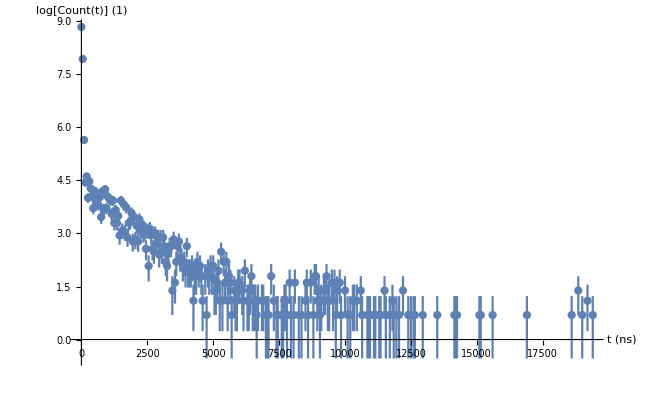

```mathematica
Show[ErrorListPlot[Tooltip[ans[[5]]]],PlotRange-> All,AxesLabel-> {"t (ns)","log[Count(t)]  (1)"},BaseStyle-> {FontSize-> 16}]
```

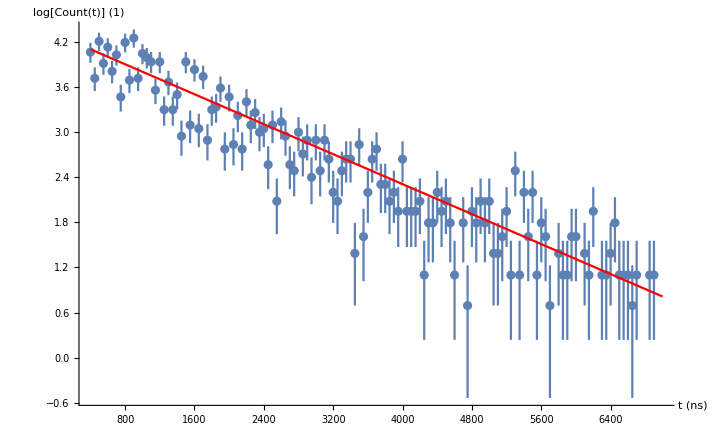

```mathematica
Show[ErrorListPlot[Tooltip[ans[[5]]]],Plot[Normal[lm],{t,startTime,endTime},PlotStyle->Red],PlotRange-> All,AxesLabel-> {"t (ns)","log[Count(t)] (1)"},BaseStyle-> {FontSize-> 16}]
```

```mathematica
{Min[mdat],Max[mdat],Length[mdat]}
```

{40.,19880.,12920}

```mathematica
Select[ans[[5]],#[[1]][[1]]==6900&]
```

{{{6900,Log[3]},ErrorBar[{Log[1-1/(√3)],Log[1+1/(√3)]}]}}

```mathematica
{startTime,endTime,binWidth}={400,6999,50};
l=#[[2]]&/@getDistList[mdat,startTime,endTime,Ceiling[(endTime-startTime)/binWidth]][[1]];
l=Select[l,#≥2&]
N[{Total[l],Mean[l]}]
```

{58,41,67,50,62,45,56,32,66,40,70,41,57,54,51,35,51,27,39,27,33,19,51,22,46,21,42,18,27,28,36,16,32,17,25,16,30,22,26,20,21,13,22,8,23,19,13,12,20,15,18,11,18,12,18,14,9,8,12,14,14,4,17,5,9,14,16,10,10,8,9,7,14,7,7,7,8,3,6,6,9,7,8,6,3,6,2,7,6,8,6,8,4,4,5,7,3,12,3,9,5,9,3,6,5,2,4,3,3,5,5,4,3,7,3,3,4,6,3,3,3,2,3,3,3}

{2220.,17.76}

```mathematica
{40.,19880.,12920}1
```

```mathematica
Normal[lm]
```

4.29835-0.000497913 t

{50,2008.38,FittedModel[4.29835-0.000497913 t],0.0000148802}

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.29835 | 0.0367837 | 116.855 | 6.71698×10^-128
t | -0.000497913 | 0.0000148802 | -33.4615 | 1.27227×10^-63

{1950.11,2070.25}

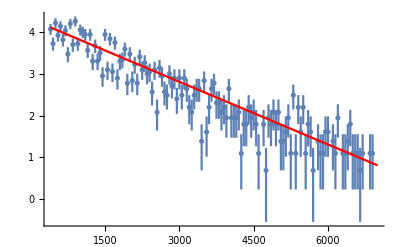

```mathematica
{startTime,endTime,binWidth}={400,6999,50};
(*{startTime,endTime,binWidth}={0,19880,50};*)
ans=plotMuon[mdat,startTime,endTime,Ceiling[(endTime-startTime)/binWidth],t,True,True];
{width=ans[[1]],lifetime=ans[[2]],lm=ans[[3]],standErr=lm["ParameterErrors"][[2]]}
lm["ParameterTable"]
{1/(1/lifetime+standErr),1/(1/lifetime-standErr)}
ans[[6]]
```

```mathematica
mdat=Import["/Users/benxgh1996/Desktop/Muon/muon_dat.xlsx",{"Data",1,Range[1,12920],1}];
```

```mathematica
mdat1=Import["/Users/benxgh1996/Desktop/Muon/muon_dat.xlsx",{"Data",2,Range[1,2769],1}];
```

```mathematica
mdat2=Import["/Users/benxgh1996/Desktop/Muon/muon_dat.xlsx",{"Data",3,Range[1,1299],1}];
```

```mathematica
mdat3=Import["/Users/benxgh1996/Desktop/Muon/muon_dat.xlsx",{"Data",4,Range[1,8852],1}];
```

{300,6000,100}

{1505.32,5.24252-0.000664312 x,101}

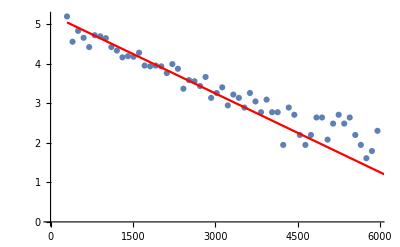

```mathematica
(*mdat*)
{startTime,endTime,binWidth}={300,6000,50}
lm=getFitModel[mdat,startTime,endTime,(endTime-startTime)/binWidth,x,True]
(*ListPlot[Tooltip@getLogList[mdat,startTime,endTime,(endTime-startTime)/binWidth][[1]]]*)
Show[ListPlot[Tooltip@getLogList[mdat,startTime,endTime,(endTime-startTime)/binWidth][[1]]],Plot[lm[[2]],{x,startTime, endTime+binWidth},PlotStyle->Red]]
```

{100,6200,400}

{2085.76,4.80055-0.000479441 x,401}

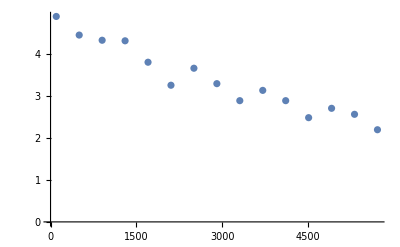

```mathematica
(*mdat1*)
{startTime,endTime,binWidth}={100,6200,400}
getFitModel[mdat1,startTime,endTime,(endTime-startTime)/binWidth,x]
ListPlot[Tooltip@getLogList[mdat1,startTime,endTime,(endTime-startTime)/binWidth][[1]]]
```

{600,9000,600}

{2410.75,4.7609-0.000414808 x,601}

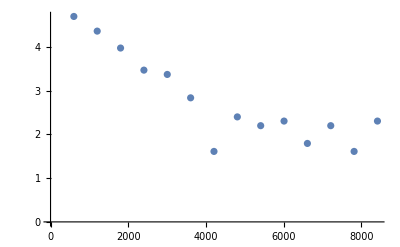

```mathematica
(*mdat2*)
{startTime,endTime,binWidth}={600,9000,600}
getFitModel[mdat2,startTime,endTime,(endTime-startTime)/binWidth,x]
ListPlot[Tooltip@getLogList[mdat2,startTime,endTime,(endTime-startTime)/binWidth][[1]]]
(*getLogList[mdat2,startTime,endTime,(endTime-startTime)/50][[1]]*)
```

19880.

{0,3000,50}

{337.867,8.02391-0.00295975 x,51}

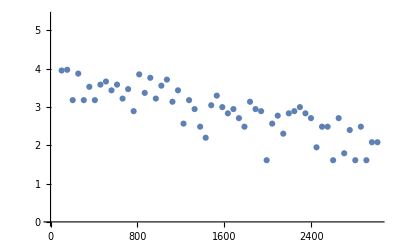

```mathematica
(*mdat3*)
Max[mdat3]
{startTime,endTime,binWidth}={0,3000,50}
getFitModel[mdat3,startTime,endTime,(endTime-startTime)/binWidth,x]
ListPlot[Tooltip@getLogList[mdat3,startTime,endTime,(endTime-startTime)/binWidth][[1]]]
```